# Part 1: Consumer

```mathematica
Clear[s]
```

```mathematica
u=s^(1/2)+c^(1/2)
```

√c+√s

```mathematica
L1=u+λ(1-pc*c-ps*s)
```

√c+√s+(1-c pc-ps s) λ

```mathematica
DLc=D[L1,c]
```

1/(2 √c)-pc λ

```mathematica
DLs=D[L1,s]
```

1/(2 √s)-ps λ

```mathematica
DLλ=D[L1,λ]
```

1-c pc-ps s

```mathematica
λ1=λ/.Solve[DLc==0,λ][[1]]
```

1/(2 √c pc)

```mathematica
λ2=λ/.Solve[DLs==0,λ][[1]]
```

1/(2 ps √s)

```mathematica
cstep1=c/.Solve[λ1/λ2==1,c][[1]]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

(ps^2 s)/pc^2

```mathematica
budget2=DLλ/.{c->cstep1}
```

1-ps s-(ps^2 s)/pc

```mathematica
ssol=s/.Solve[budget2==0,s][[1]]
```

pc/(ps (pc+ps))

```mathematica
csol=cstep1/.{s->ssol}
```

ps/(pc (pc+ps))

# Part 3 Profit

```mathematica
Clear[ac,as,ps,w,τ]
```

```mathematica
Rev=(τ*pc+1)/(pc+1)
```

(1+pc τ)/(1+pc)

```mathematica
MRev=FullSimplify[D[Rev,pc]]
```

(-1+τ)/(1+pc)^2

```mathematica
Cost=w*(τ*ssol)^(1/as)+w*((csol)^(1/ac))
```

(ps/(pc (pc+ps)))^(1/ac) w+w ((pc τ)/(ps (pc+ps)))^(1/as)

```mathematica
Profit=Rev+Cost
```

(ps/(pc (pc+ps)))^(1/ac) w+w ((pc τ)/(ps (pc+ps)))^(1/as)+(1+pc τ)/(1+pc)

```mathematica
MCost=FullSimplify[D[Cost,pc],ac>0&&ac<1&&as>0&&as<1&&pc>0&&τ>0&&τ<1]
```

(w (-as (ps/(pc (pc+ps)))^(1/ac) (2 pc+ps)+ac ps ((pc τ)/(ps (pc+ps)))^(1/as)))/(ac as pc (pc+ps))

```mathematica
ps=1;w=1
```

1

```mathematica
TeXForm[MCost]
```

\frac{\text{ac} \left(\frac{\text{pc} \tau
   }{\text{pc}+1}\right)^{\frac{1}{\text{as}}}-\text{as} (2 \text{pc}+1)
   \left(\frac{1}{\text{pc} (\text{pc}+1)}\right)^{\frac{1}{\text{ac}}}}{\text{ac}
   \text{as} \text{pc} (\text{pc}+1)}

```mathematica
ac=1/2;as=1/2;ps=1;w=1
```

1

```mathematica
FOCpi=FullSimplify[MRev==MCost]
```

(-1+τ)/(1+pc)^2==(2 (-1-2 pc+pc^4 τ^2))/(pc^3 (1+pc)^3)

```mathematica
Implicitpc=FullSimplify[MRev==MCost,1+pc>0&&τ>0&&τ<1]
```

pc^2 (1+pc-τ+pc τ (-1+2 τ))==4+2/pc

```mathematica
dpcdtau=ImplicitD[Implicitpc,pc,τ]
```

-(pc^4 (-1-pc+4 pc τ))/(2+2 pc^3+3 pc^4-2 pc^3 τ-3 pc^4 τ+6 pc^4 τ^2)

```mathematica
dpcdtau/.{pc->1}
```

-(-2+4 τ)/(7-5 τ+6 τ^2)

```mathematica
pcsols=Solve[FOCpi,pc]
```

{{pc→-(1-τ)/(4 (1-τ+2 τ^2))-1/2 √((1-τ)^2/(4 (1-τ+2 τ^2)^2)+(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))+((-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))/(3^(2/3) (-1+τ-2 τ^2)))-1/2 √((1-τ)^2/(2 (1-τ+2 τ^2)^2)-(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))-((-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))/(3^(2/3) (-1+τ-2 τ^2))-(-(1-τ)^3/((1-τ+2 τ^2)^3)+32/(1-τ+2 τ^2))/(4 √((1-τ)^2/(4 (1-τ+2 τ^2)^2)+(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))+1/(3^(2/3) (-1+τ-2 τ^2))(-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))))},{pc→-(1-τ)/(4 (1-τ+2 τ^2))-1/2 √((1-τ)^2/(4 (1-τ+2 τ^2)^2)+(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))+((-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))/(3^(2/3) (-1+τ-2 τ^2)))+1/2 √((1-τ)^2/(2 (1-τ+2 τ^2)^2)-(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))-((-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))/(3^(2/3) (-1+τ-2 τ^2))-(-(1-τ)^3/((1-τ+2 τ^2)^3)+32/(1-τ+2 τ^2))/(4 √((1-τ)^2/(4 (1-τ+2 τ^2)^2)+(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))+1/(3^(2/3) (-1+τ-2 τ^2))(-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))))},{pc→-(1-τ)/(4 (1-τ+2 τ^2))+1/2 √((1-τ)^2/(4 (1-τ+2 τ^2)^2)+(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))+((-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))/(3^(2/3) (-1+τ-2 τ^2)))-1/2 √((1-τ)^2/(2 (1-τ+2 τ^2)^2)-(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))-((-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))/(3^(2/3) (-1+τ-2 τ^2))+(-(1-τ)^3/((1-τ+2 τ^2)^3)+32/(1-τ+2 τ^2))/(4 √((1-τ)^2/(4 (1-τ+2 τ^2)^2)+(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))+1/(3^(2/3) (-1+τ-2 τ^2))(-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))))},{pc→-(1-τ)/(4 (1-τ+2 τ^2))+1/2 √((1-τ)^2/(4 (1-τ+2 τ^2)^2)+(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))+((-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))/(3^(2/3) (-1+τ-2 τ^2)))+1/2 √((1-τ)^2/(2 (1-τ+2 τ^2)^2)-(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))-((-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))/(3^(2/3) (-1+τ-2 τ^2))+(-(1-τ)^3/((1-τ+2 τ^2)^3)+32/(1-τ+2 τ^2))/(4 √((1-τ)^2/(4 (1-τ+2 τ^2)^2)+(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))+1/(3^(2/3) (-1+τ-2 τ^2))(-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))))}}

```mathematica
N[pcsols/.{τ->1/2}]
```

{{pc→-0.793701-1.37473 ⅈ},{pc→-0.793701+1.37473 ⅈ},{pc→-0.5},{pc→1.5874}}

```mathematica
N[pcsols/.{τ->1}]
```

{{pc→-0.460355-1.13932 ⅈ},{pc→-0.460355+1.13932 ⅈ},{pc→-0.474627},{pc→1.39534}}

```mathematica
pcsol=pc/.pcsols[[4]]
```

-(1-τ)/(4 (1-τ+2 τ^2))+1/2 √((1-τ)^2/(4 (1-τ+2 τ^2)^2)+(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))+((-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))/(3^(2/3) (-1+τ-2 τ^2)))+1/2 √((1-τ)^2/(2 (1-τ+2 τ^2)^2)-(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))-((-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))/(3^(2/3) (-1+τ-2 τ^2))+(-(1-τ)^3/((1-τ+2 τ^2)^3)+32/(1-τ+2 τ^2))/(4 √((1-τ)^2/(4 (1-τ+2 τ^2)^2)+(4 (-1+τ-4 τ^2))/(3^(1/3) (-1+τ-2 τ^2) (-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))+1/(3^(2/3) (-1+τ-2 τ^2))(-63+54 τ-135 τ^2+√3 √(1387-2460 τ+7602 τ^2-6460 τ^3+9915 τ^4-3072 τ^5+4096 τ^6))^(1/3))))

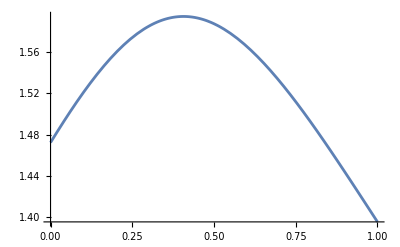

```mathematica
Plot[pcsol,{τ,0,1}]
```

```mathematica
N[pcsol/.{τ->1}]
```

1.39534

```mathematica
N[pcsol/.{τ->1/2}]
```

1.5874

```mathematica
TeXForm[pcsol]
```

-\frac{1-\tau }{4 \left(2 \tau ^2-\tau +1\right)}+\frac{1}{2} \sqrt{\frac{(1-\tau )^2}{4
   \left(2 \tau ^2-\tau +1\right)^2}+\frac{\sqrt[3]{-135 \tau ^2+\sqrt{3} \sqrt{4096
   \tau ^6-3072 \tau ^5+9915 \tau ^4-6460 \tau ^3+7602 \tau ^2-2460 \tau +1387}+54 \tau
   -63}}{3^{2/3} \left(-2 \tau ^2+\tau -1\right)}+\frac{4 \left(-4 \tau ^2+\tau
   -1\right)}{\sqrt[3]{3} \left(-2 \tau ^2+\tau -1\right) \sqrt[3]{-135 \tau ^2+\sqrt{3}
   \sqrt{4096 \tau ^6-3072 \tau ^5+9915 \tau ^4-6460 \tau ^3+7602 \tau ^2-2460 \tau
   +1387}+54 \tau -63}}}+\frac{1}{2} \sqrt{\frac{(1-\tau )^2}{2 \left(2 \tau ^2-\tau
   +1\right)^2}-\frac{\sqrt[3]{-135 \tau ^2+\sqrt{3} \sqrt{4096 \tau ^6-3072 \tau
   ^5+9915 \tau ^4-6460 \tau ^3+7602 \tau ^2-2460 \tau +1387}+54 \tau -63}}{3^{2/3}
   \left(-2 \tau ^2+\tau -1\right)}-\frac{4 \left(-4 \tau ^2+\tau -1\right)}{\sqrt[3]{3}
   \left(-2 \tau ^2+\tau -1\right) \sqrt[3]{-135 \tau ^2+\sqrt{3} \sqrt{4096 \tau
   ^6-3072 \tau ^5+9915 \tau ^4-6460 \tau ^3+7602 \tau ^2-2460 \tau +1387}+54 \tau
   -63}}+\frac{\frac{32}{2 \tau ^2-\tau +1}-\frac{(1-\tau )^3}{\left(2 \tau ^2-\tau
   +1\right)^3}}{4 \sqrt{\frac{(1-\tau )^2}{4 \left(2 \tau ^2-\tau
   +1\right)^2}+\frac{\sqrt[3]{-135 \tau ^2+\sqrt{3} \sqrt{4096 \tau ^6-3072 \tau
   ^5+9915 \tau ^4-6460 \tau ^3+7602 \tau ^2-2460 \tau +1387}+54 \tau -63}}{3^{2/3}
   \left(-2 \tau ^2+\tau -1\right)}+\frac{4 \left(-4 \tau ^2+\tau -1\right)}{\sqrt[3]{3}
   \left(-2 \tau ^2+\tau -1\right) \sqrt[3]{-135 \tau ^2+\sqrt{3} \sqrt{4096 \tau
   ^6-3072 \tau ^5+9915 \tau ^4-6460 \tau ^3+7602 \tau ^2-2460 \tau +1387}+54 \tau
   -63}}}}}